```mathematica
Remove["Global`*"]

file="iv3"
inputpath="d:\\test\\";
outputpath=inputpath<>"Edited\\";
CreateDirectory[outputpath]
rescaleV=100;
rescaleI=10000;
zeroposition=0;
```

iv3

D:\test\Edited\

```mathematica
Import and plot
```

Length of raw data: 5002

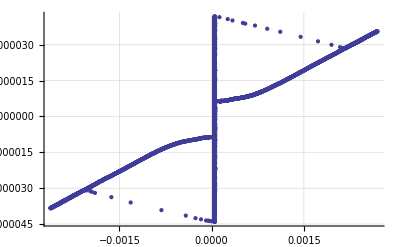

```mathematica
rawdata=Map[{N[#[[2]]/rescaleV], N[#[[4]]/rescaleI]}&,Import[inputpath<>ToString[file]<>".txt","Table"]];
Print["Length of raw data: ",Length[rawdata]];
ListPlot[{rawdata},GridLines->Automatic]
Manipulate[Show[ListPlot[{rawdata},GridLines->Automatic],PlotRange->{{xmin,xmax},{ymin,ymax}}],{xmax,0,0.01},{xmin,-0.01,0},{ymax,0,0.001}, {ymin,-0.001,0}]
```

```mathematica
Select data for Y max/min finding
```

Length of selected data: 3205

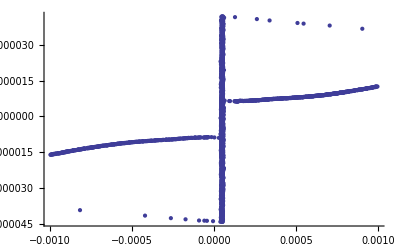

```mathematica
selectData = {};
leftX=-10*10^(-4); rightX=10*10^(-4);
For [ i = 1, i≤Length[rawdata], i++, If[rawdata[[i,1]] ≥leftX &&rawdata[[i,1]]≤ rightX,AppendTo[selectData, rawdata[[i]]] ]];
Print["Length of selected data: ",Length[selectData]];
ListPlot[selectData(*, PlotRange->{{leftX,rightX},{-0.000045,0.000045}}*)]
```

```mathematica
Find min/max and switching current
```

```mathematica
minY = Min[selectData[[All,2]]];
maxY=Max[selectData[[All,2]]];
Isw=(Abs[maxY]+Abs[minY])/2;
Print["Max=",maxY,"; Min=", minY, "; Isw(uA)=",Isw*10^6];
```

Max=0.0000418029; Min=-0.0000441184; Isw(uA)=42.9607

```mathematica
Shift along Y axis
```

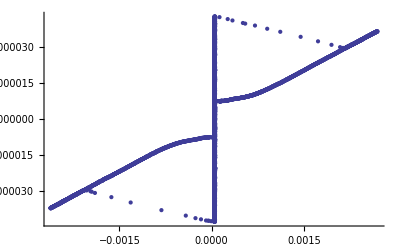

Length of Y-shifted data: 5002

d:\test\Edited\iv3_yshift.dat

```mathematica
middleY=(maxY+minY)/2;
shiftY=zeroposition-middleY;
yshiftData = {};
For [ i = 1, i≤Length[rawdata], i++, AppendTo[yshiftData, rawdata[[i]]+{0,shiftY}]];
ListPlot[yshiftData]
Print["Length of Y-shifted data: ",Length[yshiftData]];
Export[outputpath<>ToString[file]<>"_yshift.dat",Map[{N[#[[1]]], N[#[[2]]]}&,yshiftData]]
```

```mathematica
Check after Y-shifting: Select again data for Y max/min finding
```

Length of selected data: 2520

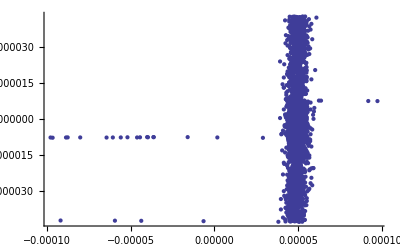

```mathematica
selectyshiftData = {};
leftX=-1*10^(-4); rightX=1*10^(-4);
For [ i = 1, i≤Length[yshiftData], i++, If[yshiftData[[i,1]] ≥leftX &&yshiftData[[i,1]]≤ rightX,AppendTo[selectyshiftData, yshiftData[[i]]] ]];
Print["Length of selected data: ",Length[selectyshiftData]];
ListPlot[selectyshiftData(*, PlotRange->{{leftX,rightX},{-0.000045,0.000045}}*)]
```

```mathematica
minY1 = Min[selectyshiftData[[All,2]]];
maxY1=Max[selectyshiftData[[All,2]]];
Isw=(Abs[maxY1]+Abs[minY1])/2;
Print["Max=",maxY1,"; Min=", minY1, "; Isw(uA)=",Isw*10^6];
```

Max=0.0000429607; Min=-0.0000429607; Isw(uA)=42.9607

```mathematica
Select data for X max/min finding
```

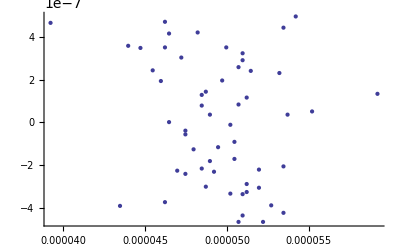

Max=0.0000592009; Min=0.0000392175

```mathematica
selectData1 = {};
minY2=-0.5*10^-6; maxY2=0.5*10^-6;
For [ i = 1, i≤Length[yshiftData], i++, If[yshiftData[[i,2]] ≥minY2 &&yshiftData[[i,2]]≤ maxY2,AppendTo[selectData1, yshiftData[[i]]] ]];
ListPlot[selectData1]

minX =Min[ selectData1[[All,1]]]; maxX=Max[selectData1[[All,1]]];
Print["Max=",maxX,"; Min=", minX];
```

```mathematica
Shift along X axis
```

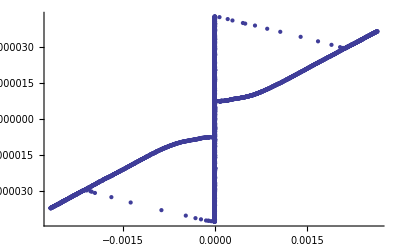

```mathematica
middleX=(maxX+minX)/2;
shiftX=0-middleX;
xyshiftData = {};
For [ i = 1, i≤Length[yshiftData], i++, AppendTo[xyshiftData, yshiftData[[i]]+{shiftX,0}]];
ListPlot[xyshiftData]
```

```mathematica
Convert IV to RI (resistance-current) presentation
```

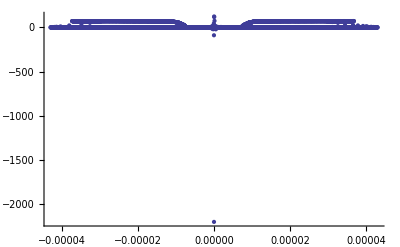

```mathematica
riData=Map[{N[#[[2]]], N[#[[1]]/#[[2]]]}&,xyshiftData];
ListPlot[riData]
```

```mathematica
Export[outputpath<>ToString[file]<>"_recalc.dat",Map[{N[#[[1]]], N[#[[2]]]}&,rawdata]];
Export[outputpath<>ToString[file]<>"_shift.dat",Map[{N[#[[1]]], N[#[[2]]]}&,xyshiftData]];
Export[outputpath<>ToString[file]<>"_ri.dat",Map[{N[#[[1]]], N[#[[2]]]}&,riData]];
Export[outputpath<>ToString[file]<>"_Isw.dat",Map[{N[#[[1]]], N[#[[2]]]}&,Isw]];
```